# Sample Code - Mathematica

Author: DS Kufel
Date: 18/11/20

### Introduction

This sample code involves two fragments of the separate codes, both of them related to my BSc dissertation about the charge-resonant-enhanced-ionization and quantum bridges in phase space.

## Calculations involving specified tridiagonal determinant of an arbitrary size

#### Defining the tridiagonal determinant

```mathematica
γ:=-1/2
```

```mathematica
α:=-116563/9531
```

```mathematica
maxbeta:=4.707
```

```mathematica
μ[α_,β_]:=1/4*(α*(α+2)+2α β-β(β+1))
```

```mathematica
upperdiagonal[R_,beta_]:=Table[(r-1)*(r-1+beta),{r,2,R}]
```

```mathematica
diagonal[R_,alpha_,beta_,gamma_,mu_]:=Table[mu-(r-1)*(r+beta+gamma)+(r-1)*(alpha),{r,1,(R),1}]
```

```mathematica
lowerdiagonal[R_,alpha_]:=Reverse[Table[(r),{r,alpha,(R-1)*alpha,alpha}]]
```

```mathematica
MM[alpha_,beta_,gamma_,mu_,Rterminate_]:=Total[{DiagonalMatrix[lowerdiagonal[Rterminate,alpha],-1],DiagonalMatrix[diagonal[Rterminate,alpha,beta,gamma,mu]],DiagonalMatrix[upperdiagonal[Rterminate,beta],1]}]
```

```mathematica
MM[Α,β,Γ,Μ,3] //MatrixForm
```

(Μ | 1+β | 0
2 Α | -2+Α-β-Γ+Μ | 2 (2+β)
0 | Α | 2 Α-2 (3+β+Γ)+Μ)

```mathematica
(* Tri-diagonal matrix reported by Downing (2013) to specify one of the conditions for the Heun's power series termination to a polynomial of degree Rterminate (see Downing,C.A.(2013), Journal of Mathematical Physics,54(7),072101; page 7) *)
```

#### Finding the determinant fulfilling certain conditions

```mathematica
Select[Select[Select[Values@Flatten[Solve[Det[MM[α,β,γ,μ[α,β],9]]==0,β]] ,Im[#]==0&],#>0 &],#<maxbeta&]
```

{Root0.310Root[9988937504302375666207090750290424759992488100247133619116334079975812115585982556806844953-19985686704032122054239432160253821522983688503647537049240387267492441961581393691234651941 #1-35780975793729533578452145127232619941964411424688470431364200693418532796562228516686599819 #1^2-12540139916370622420690020510402634960506374970001119020052936028783233398311403640295185876 #1^3+«11»+2677077896600739139355063698388004653806935874813099999701781755601426500623700 #1^15+26503813323539958421527825349161226198027621867561847173117529244785398675437 #1^16+157167149005167395001634286321304376767389448823634641661998464122586898947 #1^17+421203966049788996431080389657325985116310457732141943804188184085201241 #1^18&,13]0.3103159348300118,Root2.11Root[9988937504302375666207090750290424759992488100247133619116334079975812115585982556806844953-19985686704032122054239432160253821522983688503647537049240387267492441961581393691234651941 #1-35780975793729533578452145127232619941964411424688470431364200693418532796562228516686599819 #1^2-12540139916370622420690020510402634960506374970001119020052936028783233398311403640295185876 #1^3+«11»+2677077896600739139355063698388004653806935874813099999701781755601426500623700 #1^15+26503813323539958421527825349161226198027621867561847173117529244785398675437 #1^16+157167149005167395001634286321304376767389448823634641661998464122586898947 #1^17+421203966049788996431080389657325985116310457732141943804188184085201241 #1^18&,14]2.1073997500573074}

```mathematica
(* I am searching for such β values that make determinant of a matrix 0 and in addition which are real and fulfilling 0 < β < maxbeta  *)
```

## Wigner quasi-probability distribution in position-momentum phase space by means of numerical integration

```mathematica
Subscript[ψ, delocalized][ξ_,c_,Ω_]:=1/(√(-ExpIntegralE[-2 c Ω,2 c]+4^(-c Ω) c^(-2 c Ω) Ω Gamma[2 c Ω]))*ξ^(c Ω)*Exp[-c ξ]
```

```mathematica
(* Wavefunction to be plotted in phase-space *)
```

```mathematica
cf[u_]=Blend[{RGBColor[0.13192950331883727, 0.9998168917372396, 0.9990386816205081],RGBColor[0.1300984206912337, 0.9975127794308385, 0.481177996490425],RGBColor[0., 0., 0.],RGBColor[0.7097581445029374, 0., 0.970443274586099],RGBColor[0.9859616998550393, 0., 0.02696269169146258],RGBColor[0.9957122148470283, 0.7894560158693827, 0.04928664072632944],RGBColor[0.998992904554818, 0.9320515754940109, 0.03978027008468757]},u]
```

Blend::argl: u should be a real number or a list of non-negative numbers, which has the same length as ….

Blend[{RGBColor[0.13192950331883727, 0.9998168917372396, 0.9990386816205081],RGBColor[0.1300984206912337, 0.9975127794308385, 0.481177996490425],RGBColor[0., 0., 0.],RGBColor[0.7097581445029374, 0., 0.970443274586099],RGBColor[0.9859616998550393, 0., 0.02696269169146258],RGBColor[0.9957122148470283, 0.7894560158693827, 0.04928664072632944],RGBColor[0.998992904554818, 0.9320515754940109, 0.03978027008468757]},u]

```mathematica
(* Home-made colormap; *)
```

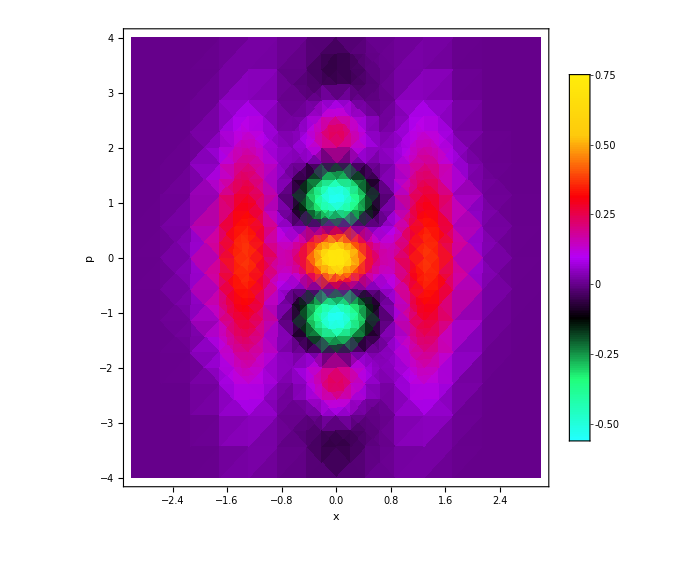

```mathematica
iF4[δ_,x_,p_,c_,Ω_]:=NDSolveValue[{F3'[δ]==1/(2*Pi)*Subscript[ψ, delocalized][1/(Cosh[x+δ])^2,c,Ω]*Subscript[ψ, delocalized][1/(Cosh[x-δ])^2,c,Ω]*Exp[2ⅈ p δ],F3[0]==1},F3,{δ,-10000,+10000}];
wignerplot=DensityPlot[Re[iF4[δ,x,p,7,1/4][10000]-iF4[δ,x,p,7,1/4][-10000]],{x,-3,3},{p,-4,4},ImageSize->Large,PlotRange->All,ImageSize->Large,ColorFunction->cf,PlotLegends->{LabelStyle->FontSize->14},FrameLabel -> {Style["x",18,Black,Bold],Style["p",18,Black,Bold]},FrameTicksStyle-> {14, 14}]
```

```mathematica
(* Wigner quasi-probability plot above *)
```

```mathematica
(* Note that the above way of calculating the definite integral is several orders of magnitude quicker compared to naively using NIntegrate! *)
```